```mathematica
(* This notebook evaluates the performance of formula inference for the FNR of the PR monitor 

This notebook assumes automatic disjunction breakup rules.
*)
```

```mathematica
(* clear all time-point detectors *) 
If[isDet[PI],Clear[ # ]& /@ (#["name"]&/@ (detSeq[PI, 1, 30] ))];
Clear[PI, prMon, winSize, allDets, allCh1s, allCh0s, allH1s, allH1sNegs];
```

Clear::ssym: PI15[name] is not a symbol or a string.

Clear::ssym: PI16[name] is not a symbol or a string.

Clear::ssym: PI17[name] is not a symbol or a string.

General::stop: Further output of Clear::ssym will be suppressed during this calculation.

```mathematica
(* parameters for the rest of this notebook *) 
winSize  = 30; 
createDet["PI"];
allDets= Join[{PI}, detSeq[PI, 1, winSize]];
allCh1s = #["ch1"]&/@ allDets;
allCh0s = #["ch0"]&/@ allDets;
allH1s = #["h1"]&/@ allDets;
allH1sNegs = Flatten@( {#["h1"], ¬#["h1"]}&/@ allDets);
(* general definition of the PR monitor *) 
prMon[t_] = ¬_w PI ∧_d ¬_s Subscript[F, 1,t] PI;
prMon[winSize];
```

```mathematica
(* a useful automatic rule *)
myCondProb[a_ ∨ b_ \[Conditioned] c_] := (myCondProb[a\[Conditioned]c] + myCondProb[b\[Conditioned]c] - myCondProb[Simplify[a∧b]\[Conditioned]c]);
```

```mathematica
(* necessary assumptions/inputs *) 
makeDetIndepOfAllGTs[#]&/@ allDets;
(* Stronger version of assumptions *) 
(* make detections independent of other ground truths, given their own ground truth and other stuff *) 
makeDetsOneVsAllStrongIndepGivenGTs[ #, Complement[allDets, {#}]]&/@allDets;
Evaluate@((fpr[#])& /@ Join[{PI},detSeq[PI, 1, winSize]]) =Table[0.1, winSize+1];
Evaluate@((myCondProb[ #["nc"] \[Conditioned]¬ #["h1"]])&/@ Join[{PI}, detSeq[PI,1, winSize]] )=Table[0.0, winSize+1];
```

Set::setraw: Cannot assign to raw object 0.1.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object 0..

General::stop: Further output of Set::setraw will be suppressed during this calculation.

```mathematica
Timing[fnr[prMon[#]]//.negateCondRule //. eventsToDNFCondExtRule//.indepCondSplitRule//. removeIrrelevantGeneralRule //. renegateCondRule //. eventsToDNFCondExtRule //.  disjCondBreakRule //. negateCondRule ]& /@ Range[2, 30]
```

```mathematica
runtimesPr= {{0.077468,0.2709999999999999},{0.120836,0.3438999999999999},{0.213083,0.4095099999999998},{0.269457,0.46855899999999995},{0.454177,0.5217030999999999},{0.511971,0.5695327899999998},{0.643198,0.6125795109999999},{0.832696,0.6513215598999998},{0.942967,0.6861894039099998},{1.124326,0.7175704635189999},{1.563636,0.7458134171670998},{1.685958,0.7712320754503899},{1.968133,0.794108867905351},{2.176359,0.8146979811148158},{2.50598,0.8332281830033341},{2.767495,0.8499053647030008},{3.020002,0.8649148282327007},{3.321562,0.8784233454094306},{3.946296,0.8905810108684876},{4.273957,0.9015229097816388},{4.547543,0.9113706188034749},{5.204524,0.9202335569231275},{5.679276,0.9282102012308147},{6.604641,0.9353891811077332},{6.783223,0.9418502629969598},{7.351833,0.9476652366972639},{8.246183,0.9528987130275375},{8.910298,0.9576088417247838},{9.370884,0.9618479575523053}}[[All, 1]]
```

{0.077468,0.120836,0.213083,0.269457,0.454177,0.511971,0.643198,0.832696,0.942967,1.12433,1.56364,1.68596,1.96813,2.17636,2.50598,2.7675,3.02,3.32156,3.9463,4.27396,4.54754,5.20452,5.67928,6.60464,6.78322,7.35183,8.24618,8.9103,9.37088}

```mathematica
runtimesPrWithDisjRule= {{0.413372,0.2709999999999999},{0.522898,0.3438999999999999},{0.654565,0.4095099999999998},{0.808749,0.46855899999999995},{0.932135,0.5217030999999999},{1.104795,0.5695327899999998},{1.251521,0.6125795109999999},{1.411005,0.6513215598999998},{1.636379,0.6861894039099998},{1.798307,0.7175704635189999},{2.261398,0.7458134171670998},{2.22953,0.7712320754503899},{2.460232,0.794108867905351},{2.675672,0.8146979811148158},{2.925257,0.8332281830033341},{3.239495,0.8499053647030008},{3.545472,0.8649148282327007},{3.951779,0.8784233454094306},{4.220415,0.8905810108684876},{4.541835,0.9015229097816388},{4.849313,0.9113706188034749},{5.305831,0.9202335569231275},{5.688498,0.9282102012308147},{6.146694,0.9353891811077332},{6.65104,0.9418502629969598},{7.210519,0.9476652366972639},{7.498123,0.9528987130275375},{7.65955,0.9576088417247838},{8.491057,0.9618479575523053}}[[All, 1]]
```

{0.413372,0.522898,0.654565,0.808749,0.932135,1.1048,1.25152,1.41101,1.63638,1.79831,2.2614,2.22953,2.46023,2.67567,2.92526,3.2395,3.54547,3.95178,4.22042,4.54184,4.84931,5.30583,5.6885,6.14669,6.65104,7.21052,7.49812,7.65955,8.49106}

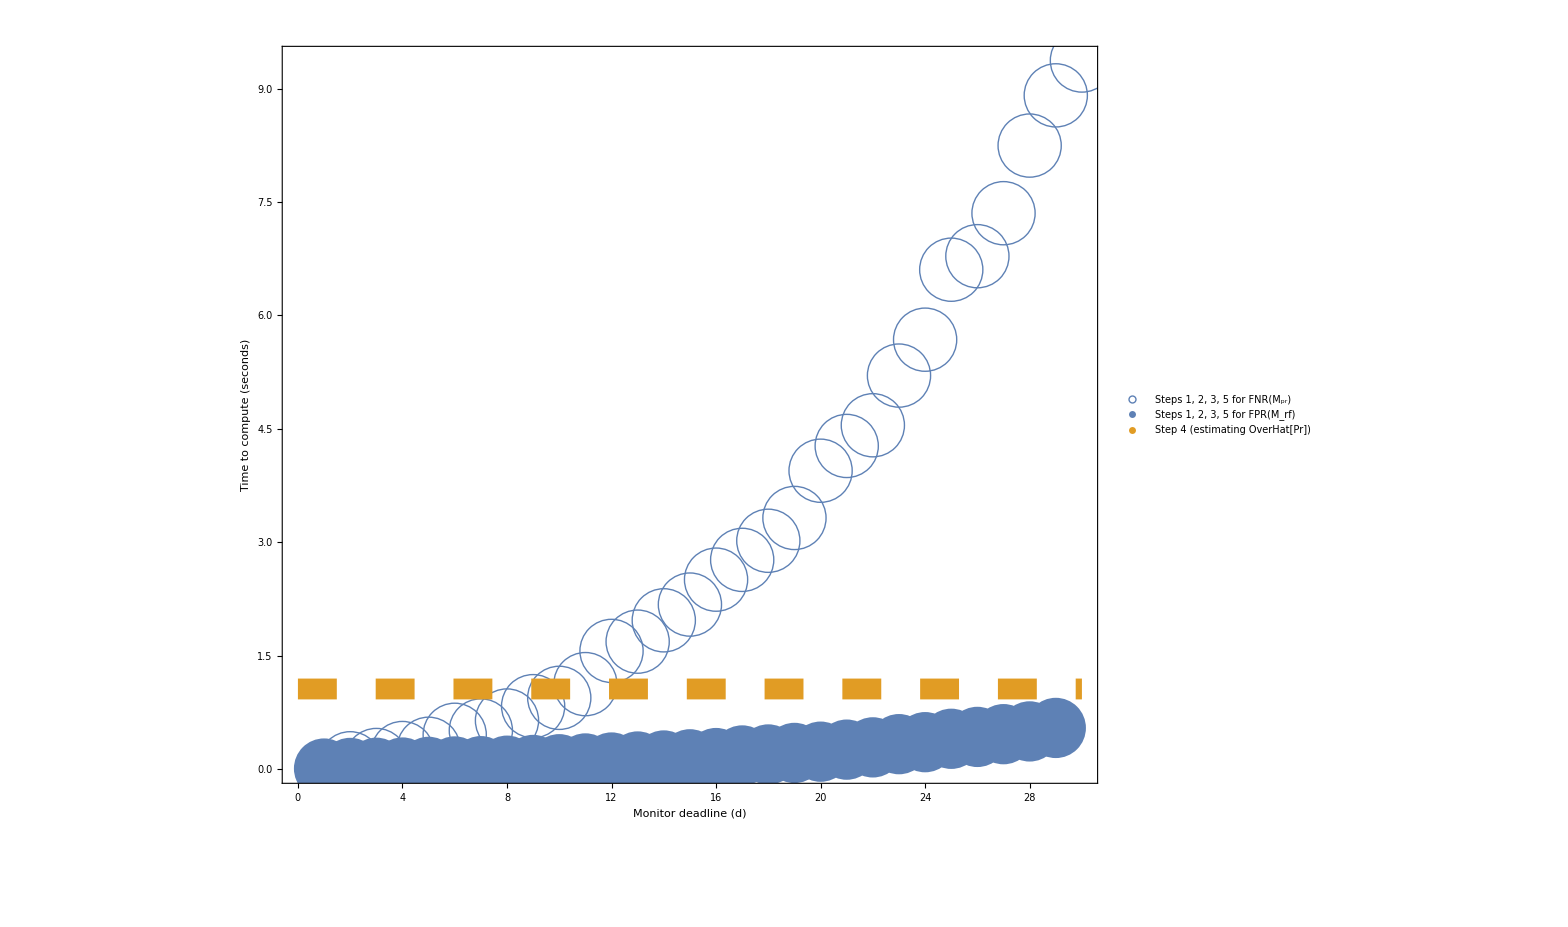

```mathematica
Legended[Show[ListPlot[{Inner[List, Range[2,30], runtimesPr, List],Inner[List, Range[1,29], runtimesRf, List]}, PlotMarkers->{Style[◦,Bold,FontSize->65, standardColors[[1]]],Style[•,Bold,FontSize->62, standardColors[[1]]]} ], chartHorLine[1.06, 30, 0, standardColors[[2]],
{Thickness[0.01](*AbsoluteThickness[6]*),AbsoluteDashing[28]}],ImageSize->1500, BaseStyle-> {FontSize->45}, Frame->True, FrameLabel->{StringJoin["Monitor deadline ", ToString[ Style["(d)", Italic], StandardForm]  ],"Time to compute (seconds)"}],Placed[PointLegend[Directive@@@{{standardColors[[1]]},  {standardColors[[2]]},{AbsoluteDashing[10],AbsoluteThickness[6], standardColors[[2]]}},{"Steps 1, 2, 3, 5 for FNR(M_pr)",StringJoin["Steps 1, 2, 3, 5 for FPR(M_rf)"],"Step 4 (estimating OverHat[Pr])" },
LegendMarkerSize->40,LegendMarkers->{Style[○,Bold,FontSize->35] ,Style[•,Bold,FontSize->50, standardColors[[1]]], Graphics[{Line[{{-10,0},{10,0}}]}](*Graphics[{Thick,SSSTriangle[1,1,1]}]*)}],{0.27,0.8}]](*, PlotMarkers->{Style[◦,Bold,FontSize->65] ,Style[△,Bold,FontSize->61]Style[•,Bold,FontSize->63]  }]*)
```